```mathematica
allFiles=FileNames["*.m",NotebookDirectory[]<>"weaveMaps/"];
```

Method to display the canvases clearly:

```mathematica
display[matrix_]:=Module[{},
output = matrix;
For[i=1,i≤Dimensions[output][[1]],i++,
output[[i,All]] = output[[i,All]]+5*Mean[output[[i,All]]];
];

Return[ArrayPlot[output, ColorFunction->"ThermometerColors"]];

];
```

This is an implementation of the pre-processing algorithm to clean up the images.

```mathematica
clean[canvas_]:=Module[{},
output =canvas;
For[i=1,i≤Dimensions[output][[1]],i++,
output[[i,All]] = output[[i,All]]-2*Mean[output[[i,All]]];
];
output = CommonestFilter[output,{1,3}];
Return[output];
];
```

This is a helper function to the distWeaveMapsZJ method that finds the minimum distance across all possible relative row placements (see below for further description).

```mathematica
minRowOverlap::usage="This function takes as input two rows of two images, then considers all possible overlaps between them and outputs the overall minimum distance based on some appropriate metric (EuclideanDistance for instance)"

minRowOverlap[row1_, row2_]:= Module[{},
	
	numCols1 = Length[row1];
	numCols2 = Length[row2];

	If[numCols1 ≥ numCols2,smallCol = row2; largeCol = row1, smallCol = row1; largeCol = row2];

	(*This is the maximum number of overlaps*)
	numPlaces = Length[largeCol]-Length[smallCol]+ 1;

	(*This adjust how many overlaps we actually compare. To increase speed of algorithm, we avoid comparing overlaps 
	that are too similar to each other by setting jumpSize > 1 *)
	jumpSize = Floor[numPlaces/10];
	min = Power[10,10];
	imin = 0;

	For[j=1, j<= 1, j=j+jumpSize,

		rowsLargeCol = largeCol[[j;;j+Length[smallCol]-1]];
		d = EuclideanDistance[rowsLargeCol,smallCol];

		If[d<min, min=d; imin = j;];	
];

(*Function outputs smallest distance across all overlaps used*)
Return[{d,imin}]
	
]
```

This function takes as input two rows of two images, then considers all possible overlaps between them and outputs the overall minimum distance based on some appropriate metric (EuclideanDistance for instance)

```mathematica
Get[allFiles[[3]]];
test1 = Transpose[matV];
Get[allFiles[[4]]];
test2 = Transpose[matV];

clean1 = clean[test1];
clean2 = clean[test2];

display[clean1]
display[clean2]


Dimensions[test1]
Dimensions[test2]
```

-Graphics-

-Graphics-

{514,405}

{442,526}

```mathematica
rowDistances::usage="This function outputs a matrix containing the minimum distance between each of the rows of the input canvases"

rowDistances[im1_,im2_]:=Module[{},
numRows1 = Dimensions[im1][[1]];
numRows2 = Dimensions[im2][[1]];

result = ConstantArray[0,{numRows1,numRows2}];
iMatrix =  ConstantArray[0,{numRows1,numRows2}];;

(*Iterates through rows of im1 and im2*)
(*For[c1=1, c1≤numRows1,c1++,
If[Divisible[c1,100],Print[c1]];

For[c2=1,c2≤ numRows2,c2++,
{result[[c1,c2]],iMatrix[[c1,c2]]} = minRowOverlap[im1[[c1,All]],im2[[c2,All]]];
];
];
*)


Return[{result,iMatrix}];
];
```

This function outputs a matrix containing the minimum distance between each of the rows of the input canvases

```mathematica
{distMatrix,iMatrix}=rowDistances[clean1,clean2];
```

100

200

300

400

500

```mathematica
minOverlapAt[distances_]:=Module[{},

rows=Dimensions[distances][[1]];
col = Dimensions[distances][[2]];
stepSize = 10;
minAt = 0;
minSum = Power[10,10];
minOverlap = 0;
thresh = col/3;

For[c3=1, c3≤ thresh,c3++,
diagonal = ConstantArray[0,{1,col}];
sum = 0;
temp = 0;
c4 = 1;
If[c3≤0.5*col,
If[c3+temp≤col && c4+temp ≤rows,
sum += distances[[c4+temp,c3+temp]];
diagonal[[1,c4]]=distances[[c4+temp,c3+temp]];
temp++;, Break[];];
];

(*Print[sum];*)
sum = sum/(temp);
(*sum= Norm[diagonal[[1,1;;temp]]]/temp;*)
If[sum<minSum, minSum=sum; minAt = c3;];

];

Return[{minAt, minSum}];
];
```

```mathematica
minOverlapAt[distMatrix]
minOverlapAt[Transpose[distMatrix]]
```

{35,17.349}

{86,24.8038}

```mathematica
ref = Line[{{0,Dimensions[test2][[1]]-35},{Dimensions[test2][[2]],Dimensions[test2][[1]]-35}}];
GraphicsRow[{Show[display[test2],Graphics[{Black,ref}]],display[test1]}]
```

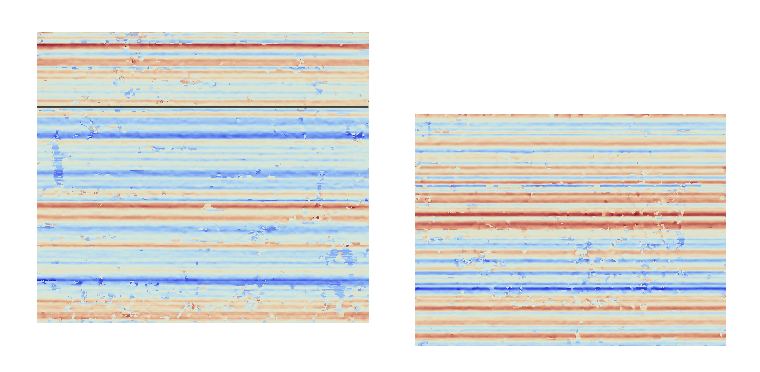

```mathematica
horizontal::usage="This function takes an image as input and ouputs the image rotated so that its stripes are horizontal"

horizontal[canvas_]:=Module[{},
lines =ImageLines[EdgeDetect[clean[canvas],1,0.1],MaxFeatures->100];
verticalCount=0;

	For[i=1,i≤Length[lines],i++,
	current=lines[[i,1]];
	
	If[Abs[current[[1,2]]-current[[2,2]]]>1 && Abs[current[[1,1]]-current[[2,1]]] < 100,
	verticalCount++;];
];
(*Depending on whether most lines are horizontal or vertical, output original or rotated image*)
If[verticalCount>Length[lines]/2,
Return[Transpose[canvas]];,
Return[canvas];]
];
```

This function takes an image as input and ouputs the image rotated so that its stripes are horizontal

```mathematica
compareAll::usage="Considers all possible orientations of images and computes minimum distance using compare method. Assumes input to have horizontal lines and uses compare method to calculate the distance using each overlap."

compareAll[clean1_,clean2_]:=Module[{},

{distMatrix,iMatrix}=rowDistances[clean1,clean2];

(*We fix im1 and rotate im2 appropriately to account for all possible orientations
For now, we ignore side roatation and focus on up and down rotation*)
r1 = Reverse[clean2];
distMatrix1 = Reverse[distMatrix,2];
(*r2 = Reverse[clean2,2]; 
r3 = Reverse[Reverse[clean2],2];*)

{min0,sum0}=minOverlapAt[distMatrix];
Print["good1"];
{min1,sum1} = minOverlapAt[Transpose[distMatrix]];
Print["good2"];
{min2,sum2} = minOverlapAt[distMatrix1];
Print["good3"];
{min3,sum3} = minOverlapAt[Transpose[distMatrix1]];

minSum = Min[sum0, sum1, sum2, sum3];

Print["zero:"];
Print[sum0];
Print[min0];

Print["first:"];
Print[sum1];
Print[min1];

Print["second:"];
Print[sum2];
Print[min2];

Print["third:"];
Print[sum3];
Print[min3];

(*third output param is 1 is image was rotated and 0 else. last output is 1 if line or alignment belongs to
image 1 and 0 if from image 2*)
If[minSum == sum0, Return[{minSum, min0,0,0}]];
If[minSum == sum1, Return[{minSum, min1,0,1}]];
If[minSum == sum2, Return[{minSum, min2,1,0}]];
If[minSum == sum3, Return[{minSum, min3,1,1}]];

];
```

Considers all possible orientations of images and computes minimum distance using compare method. Assumes input to have horizontal lines and uses compare method to calculate the distance using each overlap.

```mathematica
compareAll[clean1,clean2]
```

100

200

good1

good2

good3

zero:

9.66039

78

first:

9.67965

30

second:

9.99773

54

third:

11.1637

25

{9.66039,78,0,0}

```mathematica
ref = Line[{{0,Dimensions[test1][[1]]-8},{Dimensions[test1][[2]],Dimensions[test1][[1]]-8}}];
GraphicsRow[{Show[display[test1],Graphics[{Black,ref}]],display[test2]}]
```

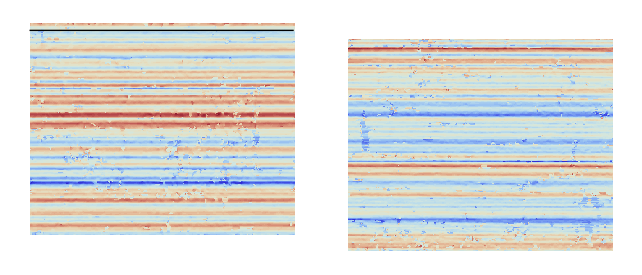

```mathematica
distWeaveMapsZJ[canvas1_, canvas2_]:=Module[{},

(*Reduce amount of noise in both images*)

(*Ensure that both inputs are oriented with horizontal stripes*)
canvas1H = horizontal[canvas1];
canvas2H = horizontal[canvas2];

(*Find the rows that are the most similar between two canvases*)
minArray = findOverlap[canvas1H, canvas2H, 4];

(*Compute the distance between images using all overlaps in minArray and pick the one with smallest distance*)
{dmin, minSubset,orientation,index} = compareAll[canvas1H,canvas2H, minArray];

Return[{dmin,minSubset,orientation,index}];
];

Get[allFiles[[3]]];
test1 = matV;
Get[allFiles[[4]]];
test2 = matV;

{dmin,minSubset,orientation,index} =distWeaveMapsZJ[test1,test2]
```